```mathematica
FileNames[NotebookDirectory[]<>"*.csv"]//TableForm
```

C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\experiment-2-elman-letter-topology-incomplete.csv
C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\experiment-2-elman-xor-initialization-incomplete.csv
C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\experiment-5-dna-pool-fawcett.csv
C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\experiment-5-dna-pool-incomplete.csv
C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\hparams_table_experiment1-A.csv
C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\hparams_table_experiment1-B.csv
C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\hparams_table_experiment1-C.csv
C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\long-lstm.csv
C:\Users\Johannes\Dropbox\University\Research\Neural Networks\qrnn\fiddle\long-rnn.csv

```mathematica
Clear[extract]
extract[data_Dataset,keys_List,value_String,collatorF_:MeanAround]:=With[
{slots=Slot/@keys},
collatorF/@data[GroupBy[(slots&)->Key[value]]]//Normal
]
extract[data_Dataset,keys_List,values_List,collatorF_:MeanAround]:=With[
{slots=Slot/@keys},
collatorF/@data[GroupBy[(slots&)->Function[sth,Table[sth[v],{v,values}]]]]//Normal
]
```

```mathematica
textStyle=Directive[{Black,FontName->"Times New Roman",FontSize->14}];
```

```mathematica
Clear[boxWhisker]
boxWhisker[data_,{key_String,label_String},roundF_:Identity,extra_:"Outliers"]:=With[{
dd=If[ListQ[data],
(extract[#,{key},"hparams/epoch",Identity]//KeyValueMap[Function[{kkey,value},{roundF@First@kkey,value}]]//SortBy[First])&/@data
,
extract[data,{key},"hparams/epoch",Identity]//KeyValueMap[Function[{kkey,value},{roundF@First@kkey,value}]]//SortBy[First]
]
},
foo=dd;
BoxWhiskerChart[If[ListQ[data],
(PadRight[#[[All,2]],20,{{}}]&/@dd)ᵀ//.{}->Nothing,
Last/@dd
],
extra,
PlotTheme->{"Detailed","Scientific"},
GridLines->{None,Automatic},
ChartLabels->If[ListQ[data],
{Union@@Map[First,dd,{2}],None},
First/@dd
],
BaseStyle->textStyle,
FrameLabel->{label,"training steps"},
FrameStyle->Black,
BarSpacing->2,
ImageSize->220,
PerformanceGoal->"Speed",
PlotRange->{All,Automatic}
]
]
```

```mathematica
Options[plotGrid]={ImagePadding->40};
plotGrid[l_List,w_,h_,opts:OptionsPattern[]]:=Module[{nx,ny,sidePadding=OptionValue[plotGrid,ImagePadding],topPadding=0,widths,heights,dimensions,positions,frameOptions=FilterRules[{opts},FilterRules[Options[Graphics],Except[{ImagePadding,Frame,FrameTicks}]]]},{ny,nx}=Dimensions[l];
widths=(w-2 sidePadding)/nx Table[1,{nx}];
widths[[1]]=widths[[1]]+sidePadding;
widths[[-1]]=widths[[-1]]+sidePadding;
heights=(h-2 sidePadding)/ny Table[1,{ny}];
heights[[1]]=heights[[1]]+sidePadding;
heights[[-1]]=heights[[-1]]+sidePadding;
positions=Transpose@Partition[Tuples[Prepend[Accumulate[Most[#]],0]&/@{widths,heights}],ny];
Graphics[Table[Inset[Show[l[[ny-j+1,i]],ImagePadding->{{If[i==1,sidePadding,0],If[i==nx,sidePadding,0]},{If[j==1,sidePadding,0],If[j==ny,sidePadding,topPadding]}},AspectRatio->Full],positions[[j,i]],{Left,Bottom},{widths[[i]],heights[[j]]}],{i,1,nx},{j,1,ny}],PlotRange->{{0,w},{0,h}},ImageSize->{w,h},Evaluate@Apply[Sequence,frameOptions]]]
```

## Parameter Initialization

```mathematica
data=Import[NotebookDirectory[]<>"experiment-2-elman-xor-initialization-incomplete.csv","Dataset","HeaderLines"->1];
```

```mathematica
(* all entries finished with low score or were cut off *)
Length[data]
Length[data[Select[#["hparams/epoch"]≥999.∨#["hparams/validate_best"]<.001&]]]
```

1643

1643

```mathematica
(* all entries are unique *)
data[GroupBy[{Slot["initial_bias"],Slot["initial_bias_spread"],Slot["initial_weights_spread"],Slot["initial_unitaries_spread"],Slot["seed"]}&->Key["hparams/epoch"]]];
Length/@%//Max
```

1

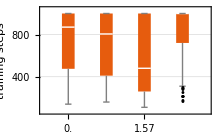
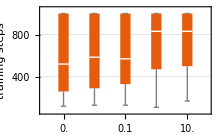
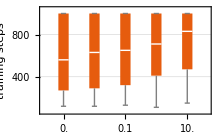
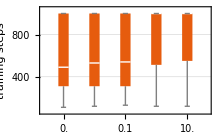

```mathematica
row1=boxWhisker[data,#,Round[#,.01]&]&/@{{"initial_bias","bias μ"},{"initial_bias_spread","bias σ"},{"initial_weights_spread","weights σ"},{ "initial_unitaries_spread","unitaries σ"}}
```

The initial bias should equal pi/2

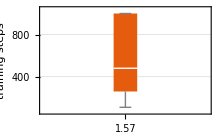
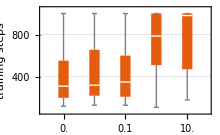
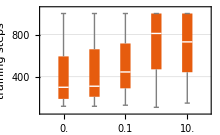
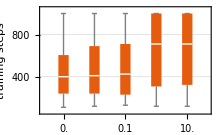

```mathematica
row2=boxWhisker[
data[Select[##["initial_bias"]==1.5708&]],
#,Round[#,.01]&
]&/@{{"initial_bias","bias μ"},{"initial_bias_spread","bias σ"},{"initial_weights_spread","weights σ"},{ "initial_unitaries_spread","unitaries σ"}}
```

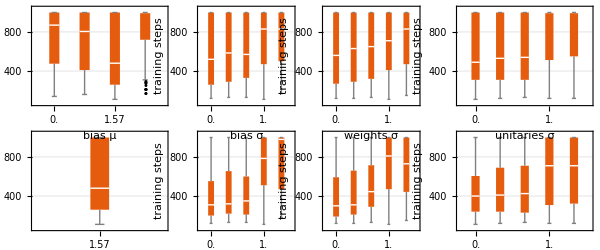

```mathematica
plotGrid[{row1,row2},600,250,ImagePadding->50]
```

All spreads should be mild

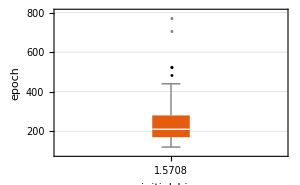
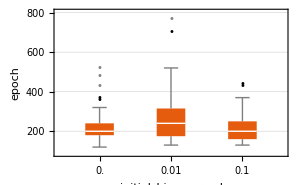
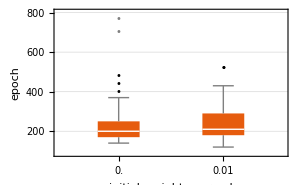
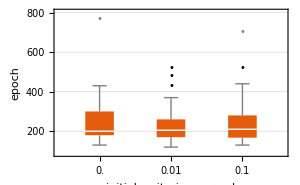

```mathematica
boxWhisker[
data[Select[#["initial_bias"]==1.5708∧#["initial_bias_spread"]<.5∧#["initial_unitaries_spread"]<.5∧#["initial_weights_spread"]<.05&]],
#
]&/@{"initial_bias","initial_bias_spread","initial_weights_spread", "initial_unitaries_spread"}
```

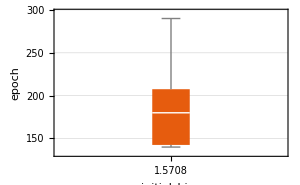
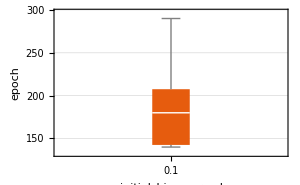
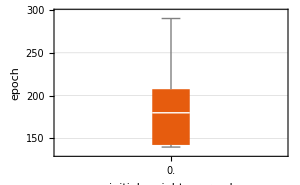
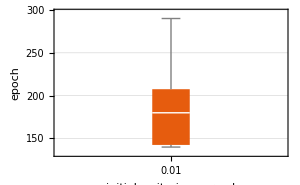

```mathematica
boxWhisker[
data[Select[#["initial_bias"]==1.5708∧#["initial_bias_spread"]==.1∧#["initial_unitaries_spread"]==.01∧#["initial_weights_spread"]==.0&]],
#
]&/@{"initial_bias","initial_bias_spread","initial_weights_spread", "initial_unitaries_spread"}
```

Best combination

```mathematica
data[GroupBy[{Slot["initial_bias"],Slot["initial_bias_spread"],Slot["initial_weights_spread"],Slot["initial_unitaries_spread"]}&->Key["hparams/epoch"]]]//SortBy[Mean]//MeanAround/@#&
```

## Topology

```mathematica
Clear[listPlot]
listPlot[data_List,{key_String,label_String},roundF_:Identity]:=With[{
dd=(extract[#,{key},"hparams/epoch",MeanAround]//KeyValueMap[Function[{kkey,value},{roundF@First@kkey,value}]]//SortBy[First])&/@data
},
foo=dd;
ListLinePlot[dd,
PlotTheme->{"Detailed","Scientific"},
GridLines->{None,Automatic},
ScalingFunctions->{Identity,Identity},
BaseStyle->textStyle,
FrameLabel->{label,"training steps"},
FrameStyle->Black,
ImageSize->300,
PerformanceGoal->"Speed",
PlotRange->{All,All},
AspectRatio->.6,
PlotStyle->{Red,Green,Blue},
BaseStyle->textStyle
]]
```

```mathematica
data=Import[NotebookDirectory[]<>"experiment-2-elman-letter-topology.csv","Dataset","HeaderLines"->1];
```

```mathematica
(* all entries finished with low score or were cut off *)
Length[data]
Length[data[Select[#["hparams/epoch"]≥999.∨#["hparams/validate_best"]<.01&]]]
```

785

785

```mathematica
(* all entries are unique *)
data[GroupBy[{Slot["workspace"],Slot["stages"],Slot["degree"],Slot["seed"]}&->Key["hparams/epoch"]]];
Length/@%//Max
```

1

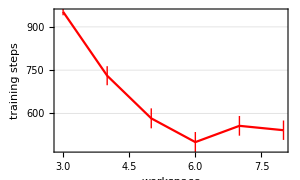
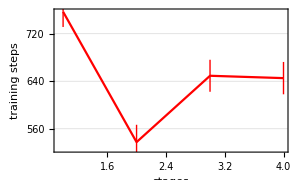
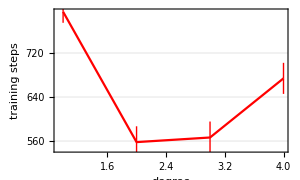

```mathematica
listPlot[{data},#,Identity]&/@{{"workspace","workspace"},{"stages","stages"},{"degree","degree"}}
```

## Long Sequence Convergence Times

```mathematica
table[pairs_]:=Grid[pairs,Spacings->{.5,.1},Alignment->Left];
```

```mathematica
Clear[listCompPlot]
listCompPlot[data_List,{key_String,label_String},roundF_:Identity]:=With[{
dd=(extract[#,{key},"hparams/epoch",MeanAround]//KeyValueMap[Function[{kkey,value},{roundF@First@kkey,value}]]//SortBy[First])&/@data
},
foo=dd;
ListLinePlot[dd,
PlotTheme->{"Detailed","Scientific"},
GridLines->{None,Automatic},
ScalingFunctions->{"Log",Identity},
BaseStyle->textStyle,
FrameLabel->{label,"training steps"},
FrameStyle->Black,
ImageSize->300,
PerformanceGoal->"Speed",
PlotRange->{All,All},
AspectRatio->.6,
PlotStyle->{Red,Green,Blue},
PlotLegends->Placed[LineLegend[{"QRNN","RNN","LSTM"},LegendLayout->table],{Scaled[{.1,.6}],{.1,.1}}],
BaseStyle->textStyle
]
]
```

```mathematica
datarnn=Import[NotebookDirectory[]<>"long-rnn.csv","Dataset","HeaderLines"->1];
(* all entries finished with low score or were cut off *)
Length[datarnn]
Length[datarnn[Select[#["hparams/epoch"]≥999.∨#["hparams/validate_best"]<.0005&]]]
(* all entries are unique *)
datarnn[GroupBy[{Slot["sentence_length"],Slot["seed"]}&->Key["hparams/epoch"]]];
Length/@%//Max
```

132

132

1

```mathematica
datalstm=Import[NotebookDirectory[]<>"long-lstm.csv","Dataset","HeaderLines"->1];
(* all entries finished with low score or were cut off *)
Length[datalstm]
Length[datalstm[Select[#["hparams/epoch"]≥999.∨#["hparams/validate_best"]<.0005&]]]
(* all entries are unique *)
datalstm[GroupBy[{Slot["sentence_length"],Slot["seed"]}&->Key["hparams/epoch"]]];
Length/@%//Max
```

189

189

1

```mathematica
data=Import[NotebookDirectory[]<>"experiment-5-dna-pool.csv","Dataset","HeaderLines"->1];
(* all entries finished with low score or were cut off *)
Length[data]
Length[data[Select[#["hparams/epoch"]≥999.∨#["hparams/validate_best"]<.0005&]]]
(* all entries are unique *)
data[GroupBy[{Slot["sentence_length"],Slot["seed"]}&->Key["hparams/epoch"]]];
Length/@%//Max
```

224

224

2

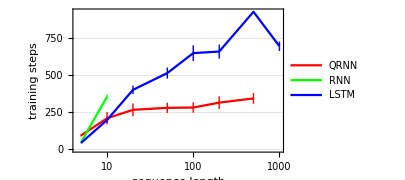

```mathematica
listCompPlot[Table[
dd[Select[#["hparams/epoch"]<999&]],{dd,{data,datarnn,datalstm}}
],
{"sentence_length","sequence length"},Round]
```

## Optimizer

```mathematica
dataA=Import[NotebookDirectory[]<>"hparams_table_experiment1-A.csv","Dataset","HeaderLines"->1];
dataB=Import[NotebookDirectory[]<>"hparams_table_experiment1-B.csv","Dataset","HeaderLines"->1];
dataC=Import[NotebookDirectory[]<>"hparams_table_experiment1-C.csv","Dataset","HeaderLines"->1];
```

```mathematica
dataP=Join[dataA,dataB,dataC]
```

<|sgd→{{0.00001,0.780.05},{0.00002,0.720.06},{0.00005,0.690.08},{0.0001,0.650.09},{0.0002,0.620.11},{0.0005,0.600.12},{0.001,0.560.14},{0.002,0.490.19},{0.005,0.470.20},{0.01,0.400.22},{0.02,0.370.22},{0.05,0.340.22},{0.1,0.290.19},{0.2,0.270.17},{0.5,0.220.18},{1.,0.000680.00022},{2.,0.090.09},{5.,0.440.04},{10.,0.540.05}},rmsprop→{{0.00001,0.670.10},{0.00002,0.640.12},{0.00005,0.530.17},{0.0001,0.410.16},{0.0002,0.330.17},{0.0005,0.260.18},{0.001,0.210.20},{0.002,0.170.16},{0.005,0.160.16},{0.01,0.0440.032},{0.02,0.0160.016},{0.05,0.000220.00007},{0.1,0.000170.00004},{0.2,0.0330.033},{0.5,0.120.12},{1.,0.400.07},{2.,0.490.04},{5.,0.440.05},{10.,0.500.07}},adam→{{0.00001,0.680.10},{0.00002,0.650.11},{0.00005,0.570.15},{0.0001,0.440.16},{0.0002,0.380.14},{0.0005,0.270.18},{0.001,0.260.18},{0.002,0.170.16},{0.005,0.0140.011},{0.01,0.170.15},{0.02,0.050.05},{0.05,0.000470.00028},{0.1,0.000200.00012},{0.2,0.000230.00007},{0.5,0.00220.0014},{1.,0.180.12},{2.,0.500.10},{5.,0.4510.017},{10.,0.470.05}}|>

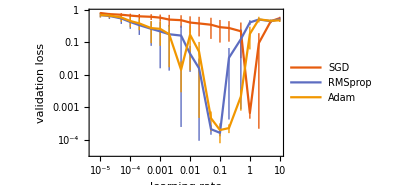

```mathematica
extract[dataP,{"optimizer","learning_rate"},"hparams/validate_best",MeanAround]//Normal//GroupBy[First@*First]//KeyValueMap[Function[{k,v},k->Sort[
Association[v]//KeyValueMap[Function[{kk,vv},{Last@kk,vv}]]
]]]//Association
ListLogLogPlot[%,Joined->True,PlotTheme->{"Scientific","Detailed"},GridLines->Automatic,FrameStyle->Directive[textStyle,Black],FrameLabel->{"learning rate","validation loss"},ImageSize->300,
PlotLegends->Placed[LineLegend[{"SGD","RMSprop","Adam"},LegendLayout->table],{Scaled[{.1,.1}],{.1,.1}}]]
```

## Postselection

```mathematica
Clear[listPlotB]
listPlotB[data_]:=
ListLinePlot[data,
PlotTheme->{"Detailed","Scientific"},
GridLines->{None,Automatic},
ScalingFunctions->{Identity,"Log"},
BaseStyle->textStyle,
FrameLabel->{"training steps","validation  loss"},
FrameStyle->Black,
ImageSize->300,
PerformanceGoal->"Speed",
PlotRange->{All,All},
AspectRatio->.6,
PlotStyle->Red,
BaseStyle->textStyle

]
```

```mathematica
dataX=Import[NotebookDirectory[]<>"postsel-simple-seq.csv","Dataset","HeaderLines"->1];
dataY=Import[NotebookDirectory[]<>"postsel-mnist.csv","Dataset","HeaderLines"->1];
```

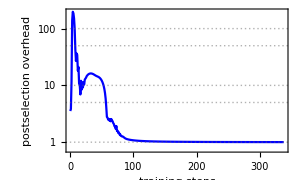

```mathematica
{Normal@dataX[All,"Step"],1/Sqrt@Normal@dataX[All,"Value"]}ᵀ//listPlotB
```

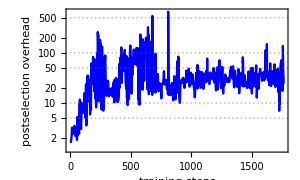

```mathematica
{Normal@dataY[All,"Step"],1/Sqrt@Normal@dataY[All,"Value"]}ᵀ//listPlotB
```

```mathematica
dataX=Import[NotebookDirectory[]<>"val-loss-simple-seq.csv","Dataset","HeaderLines"->1];
dataY=Import[NotebookDirectory[]<>"val-loss-mnist.csv","Dataset","HeaderLines"->1];
```

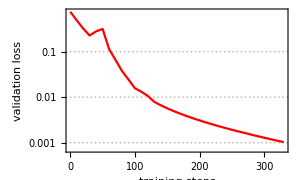

```mathematica
{Normal@dataX[All,"Step"],Normal@dataX[All,"Value"]}ᵀ//listPlotB
```

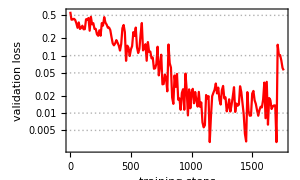

```mathematica
{Normal@dataY[All,"Step"],Normal@dataY[All,"Value"]}ᵀ//listPlotB
```